#### Q1

Find the first three roots of the Bessel function J_1(x).

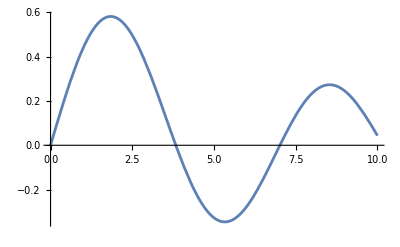

```mathematica
(* bessel function *)
J[x_]:=BesselJ[1,x]
Plot[J[x],{x,0,10}]
```

```mathematica
(* Roots *)
r1=FindRoot[J[x]==0,{x,0}]
r2=FindRoot[J[x]==0,{x,4}]
r3=FindRoot[J[x]==0,{x,7}]
```

{x→0.}

{x→3.83171}

{x→7.01559}

#### Q2

Integrate the expression f(x) = sin(x) e^-x, and then take its derivative.

```mathematica
f[x_]:=Sin[x]Exp[-x]
```

```mathematica
intf=Integrate[f[x],x]
```

-1/2 ⅇ^-x (Cos[x]+Sin[x])

```mathematica
D[intf,x]
```

-1/2 ⅇ^-x (Cos[x]-Sin[x])+1/2 ⅇ^-x (Cos[x]+Sin[x])

#### Q4

Solve the following initial-value problem using both DSolve and NDSolve. Compare your answers by plotting them.
y’’(x) - x y(x) = 0
y(0) = 1
y’(0) = - 3^(1/3)Gamma(2/3)/Gamma(1/3)

```mathematica
DSolve[{y''[x]-x*y[x]==0,y[0]==1,y'[0]==-3^(1/3)Gamma[2/3]/Gamma[1/3]},y,x]
yan=(y/.Flatten@%)[x];
(*pan=Plot[yan,{x,-10,10}]*)
```

{{y→Function[{x},3^(2/3) AiryAi[x] Gamma[2/3]]}}

```mathematica
NDSolve[{y''[x]-x*y[x]==0,y[0]==1,y'[0]==-3^(1/3)Gamma[2/3]/Gamma[1/3]},y,{x,-10,10}]
ynum=(y/.Flatten@%)[x];
(*pnum=Plot[ynum,{x,-10,10},PlotStyle->{Orange,Dashed}]*)
```

{{y→InterpolatingFunction[…]}}

```mathematica
Plot[{yan,ynum},{x,-10,10},PlotLabels->{"Analytical","Numerical"},PlotStyle->{{Green},{Blue,Dashed}}]
```

-Graphics-